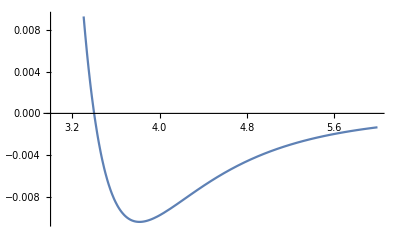

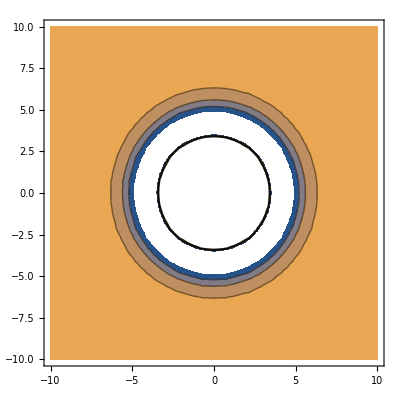

```mathematica
W[r_]=4 ϵ((σ/r)^12-(σ/r)^6);
Wv[x1_,x2_]:=W[EuclideanDistance[x1,x2]]
(* A point in space of molecule configurations is X={x1, y1, z1, x2, y2, z2, ...} *)
Ws[X_]:=Sum[Wv[X[[i]],X[[j]]],{i,1,Length[X]},{j,i+1,Length[X]}];

ϵ = 0.0104;
σ=3.40;
Plot[W[r],{r,3,6}]
ContourPlot[Wv[{0,0,0},{x,y,0}],{x,-10,10},{y,-10,10}]
```

```mathematica
CaptainKirk[n_]:=(
Reap[Sow[{0.0,0.,0.}];
If[n>1,
Sow[{x[2],0.,0.}];
];
If[n>2,
Sow[{x[3],y[3],0}];
];
If[n>3,
Do[Sow[{x[i],y[i],z[i]}],{i,4,n}];
]
][[2,1]]
)
Bones[n_]:=(
Reap[
Sow[{x[2],σ,.1 σ, 10n σ}];
If[n>2,
Sow[{x[3],σ,.1 σ, 10n σ}];
Sow[{y[3],σ,.1 σ, 10n σ}];
];

If[n>3,
start={σ,σ,σ};
Do[
Do[
Sow[{{x[i],y[i],z[i]}[[j]],start[[j]],.1σ,5 start[[j]]}];
,{j,{1,2,3}}];
start[[Mod[i-1,3]+1]]+=σ;
,{i,4,n}]
]
][[2,1]]
)
Bones[4]
CaptainKirk[4]
Ws[CaptainKirk[3]]
```

{{x[2],3.4,0.34,136.},{x[3],3.4,0.34,136.},{y[3],3.4,0.34,136.},{x[4],3.4,0.34,17.},{y[4],3.4,0.34,17.},{z[4],3.4,0.34,17.}}

{{0.,0.,0.},{x[2],0.,0.},{x[3],y[3],0},{x[4],y[4],z[4]}}

0.0416 ((2.38642×10^6)/((0.+Abs[0.-x[2]]^2)^6)-1544.8/((0.+Abs[0.-x[2]]^2)^3))+0.0416 ((2.38642×10^6)/((0.+Abs[0.-x[3]]^2+Abs[0.-y[3]]^2)^6)-1544.8/((0.+Abs[0.-x[3]]^2+Abs[0.-y[3]]^2)^3))+0.0416 ((2.38642×10^6)/((0.+Abs[x[2]-x[3]]^2+Abs[0.-y[3]]^2)^6)-1544.8/((0.+Abs[x[2]-x[3]]^2+Abs[0.-y[3]]^2)^3))

```mathematica
Engage[n_]:=(
sol[n]=FindMinimum[
Ws[CaptainKirk[n]],Bones[n]
 ];
{Graphics3D[{PointSize[0.1],Point[CaptainKirk[n]/.sol[n][[2]]]},Axes->True],sol[n][[1]]}
)
```

```mathematica
Quiet[Engage[#]&/@Range[1,20]]
```

{{-Graphics3D-,0.},{-Graphics3D-,-0.0104},{-Graphics3D-,-0.0312},{-Graphics3D-,-0.0624},{-Graphics3D-,-0.0946801},{-Graphics3D-,-0.12795},{-Graphics3D-,-0.161544},{-Graphics3D-,-0.195293},{-Graphics3D-,-0.229127},{-Graphics3D-,-0.274499},{-Graphics3D-,-0.306316},{-Graphics3D-,-0.265041},{-Graphics3D-,-0.335609},{-Graphics3D-,-0.410893},{-Graphics3D-,-0.427083},{-Graphics3D-,-0.481251},{-Graphics3D-,-0.502587},{-Graphics3D-,-0.466053},{-Graphics3D-,-0.537512},{-Graphics3D-,-0.520961}}

```mathematica
enterp=Import["enterp4.3ds",Lighting->{{"Directional", White, {0, 0, 3}}},ImageSize->Automatic]
```

-Graphics3D-

```mathematica
FindMinimum[W[r],{r,1,10}]
```

{-0.0104,{r→3.81637}}